## Lesson

Values joined by a line:

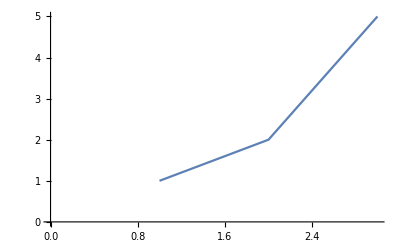

```mathematica
ListLinePlot[{1,2,5}]
```

Bar chart (values give bar heights):

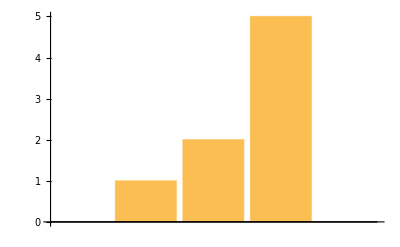

```mathematica
BarChart[{1,2,5}]
```

Pie chart (values give wedge sizes):

```mathematica
PieChart[{1,2,5}]
```

-Graphics-

Numbers arranged on a line:

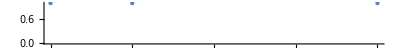

```mathematica
NumberLinePlot[{1,2,5}]
```

Elements displayed in a column:

```mathematica
Column[{1,2,5}]
```

1
2
5

## Questions

Q1. Make a bar chart of {1, 1, 2, 3, 5}.

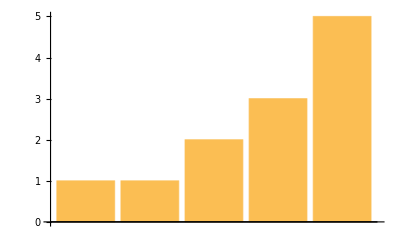

```mathematica
BarChart[{1,1,2,3,5}]
```

Q2. Make a pie chart of numbers from 1 to 10.

```mathematica
PieChart[Range[10]]
```

-Graphics-

Q3. Make a bar chart of numbers counting down from 20 to 1.

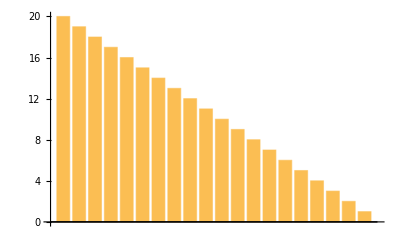

```mathematica
BarChart[Reverse[Range[20]]]
```

Q4. Display numbers from 1 to 5 in a column.

```mathematica
Column[Range[5]]
```

1
2
3
4
5

Q5. Make a number line plot of the squares {1, 4, 9, 16, 25}.

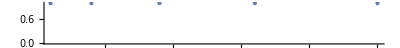

```mathematica
NumberLinePlot[Range[5]^2]
```

Q6. Make a pie chart with 10 identical segments, each of size 1.

```mathematica
PieChart[ConstantArray[1,10]]
```

-Graphics-

Q7. Make a column of pie charts with 1, 2 and 3 identical segments.

```mathematica
Column[PieChart/@Table[ConstantArray[1,i],{i,3}]]
```

-Graphics-

## Extended Questions

+Q1. Make a list of pie charts with 1, 2 and 3 identical segments.

```mathematica
PieChart/@Table[ConstantArray[1,i],{i,3}]
```

{-Graphics-,-Graphics-,-Graphics-}

+Q2. Make a bar chart of the sequence 1, 2, 3, ..., 9, 10, 9, 8, 7, ..., 1.

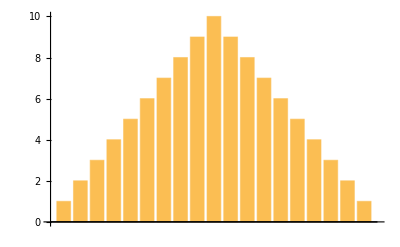

```mathematica
BarChart[Join[Range[10],Reverse[Range[9]]]]
```

+Q3. Make a list of a pie chart, bar chart and line plot of the numbers from 1 to 10.

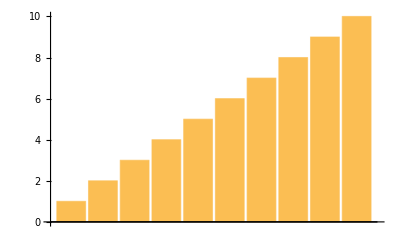
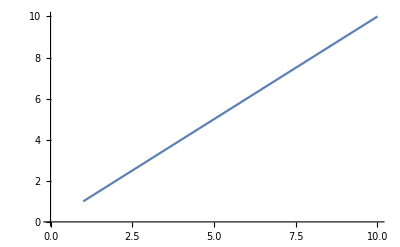
{{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
{PieChart[#],BarChart[#],ListLinePlot[#]}&/@{Range[10]}
```

+Q4. Make a list of a pie chart and a bar chart of {1, 1, 2, 3, 5, 8, 13, 21, 34, 55}.

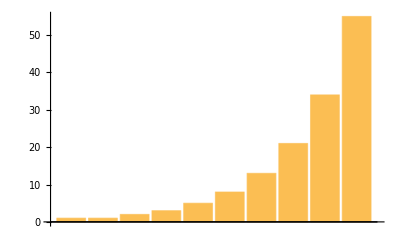
{{-Graphics-,-Graphics-}}

```mathematica
{PieChart[#],BarChart[#]}&/@{Fibonacci[Range[10]]}
```

+Q5. Make a column of two number line plots of {1, 2, 3, 4, 5}.

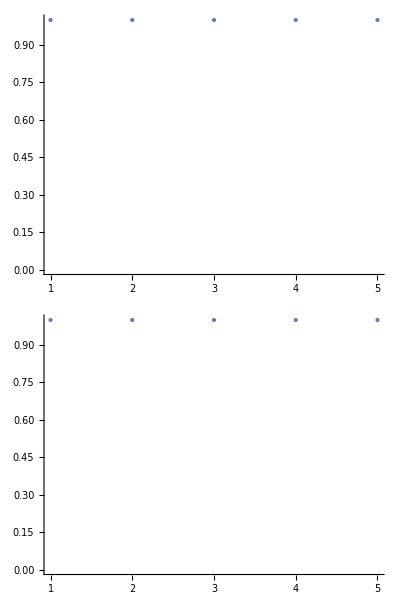

```mathematica
Column[ConstantArray[NumberLinePlot[Range[5]],2]]
```

+Q6. Make a number line of fractions 1/2, 1/3, ... through 1/9.

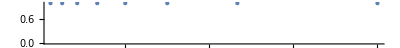

```mathematica
NumberLinePlot[1/Range[2,9]]
```